# Pressure sensor transfer function

## Supplementary information in the article

```mathematica
eqn=a(b p^(-1/2)-1)ⅇ^(√(c p))+d
values={a->106,b->50,c->328/1000,d->15}
```

d+a ⅇ^(√(c p)) (-1+b/(√p))

{a→106,b→50,c→41/125,d→15}

## Fit to data

### Read data

```mathematica
FileNames[]
```

{b_source_magic.sch,b_source_magic.spice,GTac data (1).csv,GTac data.ods,GTac data.pdf,GTac data.png,piezoresistor.sch,PressureXferFunction.nb,PressureXferFunctionStrongInv.nb,PressureXferFunctionStrongInv.pdf,PressureXferFunctionWeakInv.nb,PressureXferFunctionWeakInv.pdf}

```mathematica
datafile=Import["GTac data (1).csv"];
```

```mathematica
Dimensions[datafile]
```

{265,4}

#### Format data

```mathematica
rloading=N[ToExpression[Select[Take[#,2]&/@Rest[datafile],#≠List["",""]&]]];
runloading=N[ToExpression[Take[#,-2]&/@Rest[datafile]]];
```

```mathematica
TableForm[rloading]
```

0. | 755630.
0. | 762461.
0. | 743565.
0. | 731584.
0. | 734667.
0. | 737596.
0. | 723873.
0. | 666373.
0. | 704409.
0. | 711425.
0. | 677648.
0. | 548971.
0. | 540370.
0. | 602363.
0. | 602543.
0. | 520971.
0. | 629583.
0.27778 | 280738.
0.27778 | 273080.
0.27778 | 310674.
0.27778 | 304526.
0.27778 | 268554.
0.27778 | 257344.
0.27778 | 244942.
0.27778 | 252559.
0.27778 | 241120.
0.27778 | 250703.
0.27778 | 284765.
0.27778 | 267133.
0.27778 | 311017.
0.27778 | 321863.
0.27778 | 277075.
0.27778 | 281504.
0.27778 | 315674.
0.27778 | 306334.
0.27778 | 307020.
0.27778 | 260500.
0.27778 | 237021.
0.27778 | 232603.
0.55556 | 234378.
0.55556 | 205809.
0.55556 | 178820.
0.55556 | 129510.
0.55556 | 120608.
0.55556 | 103850.
0.55556 | 94425.4
0.55556 | 83944.4
0.55556 | 79801.1
0.55556 | 70012.5
0.83333 | 73911.6
0.83333 | 70408.9
0.83333 | 65288.5
0.83333 | 57388.7
0.83333 | 50905.2
0.83333 | 43605.2
1.11111 | 41246.1
1.11111 | 33957.2
1.11111 | 30476.8
1.11111 | 29889.8
1.11111 | 25882.3
1.38889 | 23493.
1.38889 | 19662.8
1.38889 | 19812.8
1.66667 | 15600.4
1.66667 | 14783.8
1.94444 | 12260.
1.94444 | 12346.1
2.22222 | 10834.3
2.22222 | 10099.8
2.5 | 8378.45
2.77778 | 6479.41
2.77778 | 5895.65
3.05556 | 5011.53
3.33333 | 4220.7
3.61111 | 3646.23
3.88889 | 3161.01
4.16667 | 2671.08
4.44444 | 2393.92
4.72222 | 2222.94
5.27778 | 1975.74
5.55556 | 1719.4
5.83333 | 1517.58
6.38889 | 1390.91
6.66667 | 1258.79
7.22222 | 1116.09
7.5 | 1017.93
7.77778 | 915.923
8.33333 | 798.303
8.61111 | 762.393
9.16667 | 697.225
9.72222 | 639.089
10. | 589.006
10.5556 | 549.257
11.1111 | 506.782
11.3889 | 468.183
11.9444 | 431.043
12.5 | 407.943
12.7778 | 375.232
13.3333 | 355.625
13.6111 | 338.712
13.8889 | 324.192
14.4444 | 312.893
14.4444 | 299.563
14.7222 | 291.3
15. | 282.899
15. | 275.275
15.2778 | 269.113
15.5556 | 265.073
15.5556 | 258.519
15.8333 | 251.582
16.1111 | 245.58
16.3889 | 239.119
16.9444 | 231.403
17.5 | 221.542
18.0556 | 212.731
18.6111 | 204.353
19.1667 | 194.72
19.7222 | 185.018
20.2778 | 176.687
21.1111 | 168.629
21.6667 | 160.731
22.2222 | 153.518
23.0556 | 147.355
23.8889 | 140.713
24.4444 | 134.892
25.2778 | 129.596
25.8333 | 125.396
26.3889 | 120.557
27.2222 | 115.169
28.0556 | 110.581
28.8889 | 106.016
29.7222 | 103.003
30.2778 | 99.3508
31.1111 | 94.3037
31.9444 | 92.0072
32.7778 | 89.0712
33.6111 | 85.6818
34.4444 | 83.2188
35.2778 | 80.3719
36.3889 | 77.9069
37.2222 | 75.4462
38.0556 | 72.9876
39.1667 | 70.6801
40.2778 | 68.9153
40.8333 | 67.3882
41.9444 | 65.6716
42.7778 | 63.9644
43.8889 | 62.3618
44.7222 | 60.7343
45.8333 | 59.3464
46.9444 | 57.6365
47.7778 | 56.4816
48.8889 | 55.1828
50. | 54.1328
51.1111 | 52.8133
52.2222 | 51.7222
53.0556 | 50.8616
54.1667 | 49.8161
55.2778 | 48.9511
56.3889 | 47.9489
57.2222 | 47.0905
58.3333 | 46.3875
59.4444 | 45.6569
60.2778 | 44.8353
61.3889 | 44.0113
62.5 | 43.4041
63.3333 | 42.8836
64.1667 | 42.2924
65.2778 | 41.7605
66.3889 | 41.2606
67.5 | 40.7516
68.3333 | 40.1604
69.1667 | 39.7745
70.2778 | 39.3043
71.1111 | 38.8911
72.2222 | 38.43
73.3333 | 38.058
74.1667 | 37.6882
75. | 37.323
75.8333 | 36.9713
76.3889 | 36.7089
76.9444 | 36.419
77.5 | 36.2478
77.7778 | 36.0287
78.3333 | 35.8597
78.6111 | 35.6359
78.8889 | 35.4899
79.1667 | 35.3849
79.4444 | 35.1726
80. | 35.0129
80.5556 | 34.8759
81.3889 | 34.6796
81.6667 | 34.5244
82.7778 | 34.2914
83.6111 | 34.1089
84.4444 | 33.8943
85.2778 | 33.6752
86.3889 | 33.4812
87.2222 | 33.2415
88.3333 | 33.052
89.1667 | 32.8055
90. | 32.6137
91.1111 | 32.365
92.2222 | 32.1959
93.0556 | 32.0317
94.1667 | 31.8126
95. | 31.655
96.1111 | 31.4724
96.9444 | 31.3012
98.0556 | 31.114
99.1667 | 30.9018
100.278 | 30.7465
101.389 | 30.4908
102.222 | 30.3607
103.333 | 30.1644
104.444 | 30.0024
105.556 | 29.8197
106.667 | 29.6303
107.778 | 29.4591
108.889 | 29.2809
110.278 | 29.1258
111.389 | 28.9615
112.222 | 28.845
113.611 | 28.6601
114.722 | 28.4911
116.111 | 28.3337
117.222 | 28.2241
118.611 | 28.0963
119.722 | 27.9365
121.111 | 27.7972
122.222 | 27.6831
123.611 | 27.5005
124.722 | 27.4023
125.833 | 27.3179
127.222 | 27.1787
128.333 | 27.0577
129.722 | 26.9344
131.111 | 26.802
132.222 | 26.7084
133.611 | 26.5646
135. | 26.4459
136.389 | 26.3866
137.5 | 26.2998
138.611 | 26.1971
140.556 | 26.1309
140.556 | 26.0259
140.556 | 26.019
140.556 | 25.9437
140.556 | 25.9232
140.278 | 25.914
140.278 | 25.8775
140.278 | 25.8318
140.278 | 25.8135
140.278 | 25.8044
140.278 | 25.841
140.278 | 25.7794

```mathematica
TableForm[runloading]
```

140. | 25.7771
140. | 25.72
140. | 25.7313
140. | 25.7063
140. | 25.7017
140. | 25.7314
139.722 | 25.6903
139.722 | 25.6881
139.444 | 25.6561
139.444 | 25.6903
138.889 | 25.688
138.333 | 25.6401
137.778 | 25.6767
137.222 | 25.6949
136.389 | 25.6721
135.556 | 25.6561
135. | 25.6652
134.167 | 25.6767
133.611 | 25.6902
132.778 | 25.679
131.944 | 25.7588
131.111 | 25.784
130.278 | 25.7473
129.444 | 25.7497
128.333 | 25.809
127.5 | 25.8638
126.389 | 25.8296
125.556 | 25.9186
124.722 | 25.9323
123.889 | 25.9642
122.778 | 25.9894
121.667 | 25.9939
120.833 | 26.0555
119.722 | 26.0967
118.889 | 26.1606
118.056 | 26.2131
116.944 | 26.2702
115.833 | 26.3569
115. | 26.4162
113.889 | 26.4253
113.333 | 26.4824
112.5 | 26.5395
111.667 | 26.592
111.111 | 26.6376
110.556 | 26.6833
110.278 | 26.7176
109.722 | 26.7267
109.444 | 26.7723
109.167 | 26.8043
108.611 | 26.8088
108.333 | 26.8636
108.056 | 26.8888
107.5 | 26.9002
106.667 | 26.9755
106.111 | 27.0234
105.556 | 27.101
104.444 | 27.1946
103.611 | 27.2699
102.778 | 27.3636
101.944 | 27.4137
100.833 | 27.5805
100. | 27.6261
99.1667 | 27.7722
98.3333 | 27.8566
97.2222 | 27.989
96.3889 | 28.0552
95.5556 | 28.2241
94.7222 | 28.3108
93.8889 | 28.4638
93.0556 | 28.6213
91.9444 | 28.7126
91.1111 | 28.8678
90. | 29.0391
89.1667 | 29.1875
88.3333 | 29.3244
87.2222 | 29.4956
86.3889 | 29.6736
85.2778 | 29.8472
84.4444 | 29.9978
83.6111 | 30.2078
82.5 | 30.3767
81.3889 | 30.6073
80.5556 | 30.8447
79.4444 | 31.1095
78.3333 | 31.3125
77.5 | 31.5865
76.3889 | 31.8171
75.2778 | 32.1115
74.1667 | 32.4814
72.7778 | 32.7667
71.6667 | 33.1
70.5556 | 33.4812
69.7222 | 33.7391
68.6111 | 34.1407
67.5 | 34.5495
66.1111 | 34.974
65. | 35.4352
63.8889 | 35.9738
62.7778 | 36.5514
61.6667 | 36.8778
60.5556 | 37.4097
59.1667 | 38.0876
58.0556 | 38.7405
56.9444 | 39.2724
55.8333 | 39.8909
54.7222 | 40.5416
53.6111 | 41.2861
52.5 | 41.9226
51.3889 | 42.7215
50.5556 | 43.3629
49.4444 | 44.1618
48.3333 | 45.1754
47.2222 | 46.3693
46.1111 | 47.3599
45. | 48.0927
44.1667 | 49.3094
43.0556 | 50.3594
41.9444 | 51.5577
41.1111 | 52.6031
40. | 53.7469
39.4444 | 55.0046
38.6111 | 55.9042
38.0556 | 56.9911
37.5 | 57.6982
36.9444 | 58.5199
36.6667 | 59.2071
36.3889 | 59.5403
36.1111 | 60.127
35.8333 | 60.6475
35.5556 | 60.958
35.2778 | 61.6269
35. | 62.2363
34.7222 | 63.1242
34.1667 | 64.1583
33.6111 | 65.197
32.7778 | 66.756
32.2222 | 68.7075
31.3889 | 70.632
30.5556 | 72.7549
29.7222 | 76.0306
28.8889 | 78.482
28.3333 | 80.306
27.5 | 83.7507
26.6667 | 86.6473
25.8333 | 90.1032
25.2778 | 93.8081
24.4444 | 97.2637
23.8889 | 101.138
23.0556 | 104.471
22.5 | 108.362
21.6667 | 114.391
21.3889 | 118.109
20.5556 | 124.049
20. | 130.397
19.1667 | 137.378
18.6111 | 145.477
18.0556 | 150.671
17.5 | 160.388
16.9444 | 168.117
16.1111 | 177.978
15.5556 | 188.008
15. | 200.667
14.4444 | 210.528
13.8889 | 223.182
13.3333 | 237.467
12.7778 | 255.638
12.2222 | 275.635
11.6667 | 290.144
11.3889 | 314.287
10.8333 | 343.533
10.2778 | 374.797
9.72222 | 407.879
9.16667 | 437.92
8.88889 | 479.046
8.33333 | 511.666
8.05556 | 565.511
7.5 | 612.479
7.22222 | 685.975
6.66667 | 759.055
6.38889 | 836.658
5.83333 | 947.192
5.55556 | 1044.94
5.27778 | 1182.75
5. | 1298.15
4.44444 | 1441.2
4.16667 | 1591.59
3.88889 | 1762.4
3.61111 | 2317.89
3.33333 | 2503.22
3.33333 | 2791.01
3.05556 | 3163.73
2.77778 | 3555.41
2.5 | 3942.9
2.5 | 4589.
2.22222 | 5352.83
2.22222 | 6339.37
1.94444 | 7239.14
1.94444 | 8150.34
1.66667 | 9164.65
1.66667 | 10110.
1.38889 | 10757.6
1.38889 | 11925.4
1.38889 | 12699.
1.38889 | 12776.4
1.38889 | 13331.6
1.11111 | 13527.
1.11111 | 14032.8
1.11111 | 14938.1
1.11111 | 15610.
1.11111 | 15778.8
1.11111 | 16076.3
1.11111 | 20321.9
1.11111 | 20938.
1.11111 | 21658.7
0.83333 | 24542.4
0.83333 | 27280.4
0.83333 | 31097.4
0.83333 | 32211.3
0.83333 | 39542.1
0.83333 | 44730.
0.55556 | 50463.8
0.55556 | 52281.1
0.55556 | 57239.9
0.55556 | 64154.1
0.55556 | 72443.5
0.55556 | 76365.8
0.55556 | 81944.1
0.55556 | 89370.4
0.27778 | 96999.2
0.27778 | 101964.
0.27778 | 110392.
0.27778 | 108115.
0.27778 | 106572.
0.27778 | 97606.
0.27778 | 102995.
0.27778 | 104789.
0.27778 | 107872.
0. | 105461.
0.27778 | 103251.
0.27778 | 107168.
0.27778 | 132501.
0. | 133173.
0. | 132349.
0. | 158902.
0. | 170973.
0. | 275044.
0. | 242632.
0. | 306539.
0. | 504569.
0. | 543111.
0. | 518795.
0. | 563280.
0. | 577225.
0. | 517104.
0. | 596054.
0. | 657947.
0. | 660491.
0. | 671620.
0. | 600382.
0. | 735516.
0. | 633103.
0. | 600426.
0. | 610704.
0. | 781415.

### Transform resistance into conductance

```mathematica
gloading=({#⟦1⟧,1/#⟦2⟧}&/@rloading)/. 0.0->1.*^-10;
gunloading=({#⟦1⟧,1/#⟦2⟧}&/@runloading)/. 0.0->1.*^-10;
```

```mathematica
TableForm[gloading]
```

1.×10^-10 | 1.3234×10^-6
1.×10^-10 | 1.31154×10^-6
1.×10^-10 | 1.34487×10^-6
1.×10^-10 | 1.3669×10^-6
1.×10^-10 | 1.36116×10^-6
1.×10^-10 | 1.35576×10^-6
1.×10^-10 | 1.38146×10^-6
1.×10^-10 | 1.50066×10^-6
1.×10^-10 | 1.41963×10^-6
1.×10^-10 | 1.40563×10^-6
1.×10^-10 | 1.47569×10^-6
1.×10^-10 | 1.82159×10^-6
1.×10^-10 | 1.85059×10^-6
1.×10^-10 | 1.66013×10^-6
1.×10^-10 | 1.65963×10^-6
1.×10^-10 | 1.91949×10^-6
1.×10^-10 | 1.58835×10^-6
0.27778 | 3.56205×10^-6
0.27778 | 3.66193×10^-6
0.27778 | 3.21881×10^-6
0.27778 | 3.28379×10^-6
0.27778 | 3.72364×10^-6
0.27778 | 3.88586×10^-6
0.27778 | 4.0826×10^-6
0.27778 | 3.95948×10^-6
0.27778 | 4.14732×10^-6
0.27778 | 3.98879×10^-6
0.27778 | 3.51166×10^-6
0.27778 | 3.74346×10^-6
0.27778 | 3.21526×10^-6
0.27778 | 3.10691×10^-6
0.27778 | 3.60913×10^-6
0.27778 | 3.55235×10^-6
0.27778 | 3.16782×10^-6
0.27778 | 3.26441×10^-6
0.27778 | 3.25712×10^-6
0.27778 | 3.83877×10^-6
0.27778 | 4.21904×10^-6
0.27778 | 4.29917×10^-6
0.55556 | 4.26661×10^-6
0.55556 | 4.85887×10^-6
0.55556 | 5.59223×10^-6
0.55556 | 7.72144×10^-6
0.55556 | 8.29134×10^-6
0.55556 | 9.62924×10^-6
0.55556 | 0.0000105904
0.55556 | 0.0000119126
0.55556 | 0.0000125312
0.55556 | 0.0000142832
0.83333 | 0.0000135297
0.83333 | 0.0000142028
0.83333 | 0.0000153166
0.83333 | 0.000017425
0.83333 | 0.0000196444
0.83333 | 0.000022933
1.11111 | 0.0000242447
1.11111 | 0.0000294488
1.11111 | 0.0000328118
1.11111 | 0.0000334563
1.11111 | 0.0000386365
1.38889 | 0.0000425659
1.38889 | 0.0000508575
1.38889 | 0.0000504723
1.66667 | 0.000064101
1.66667 | 0.0000676416
1.94444 | 0.000081566
1.94444 | 0.0000809976
2.22222 | 0.0000922995
2.22222 | 0.0000990122
2.5 | 0.000119354
2.77778 | 0.000154335
2.77778 | 0.000169616
3.05556 | 0.00019954
3.33333 | 0.000236927
3.61111 | 0.000274256
3.88889 | 0.000316354
4.16667 | 0.000374381
4.44444 | 0.000417726
4.72222 | 0.000449854
5.27778 | 0.000506139
5.55556 | 0.000581599
5.83333 | 0.000658943
6.38889 | 0.000718952
6.66667 | 0.000794416
7.22222 | 0.000895983
7.5 | 0.000982382
7.77778 | 0.0010918
8.33333 | 0.00125266
8.61111 | 0.00131166
9.16667 | 0.00143426
9.72222 | 0.00156473
10. | 0.00169778
10.5556 | 0.00182064
11.1111 | 0.00197323
11.3889 | 0.00213592
11.9444 | 0.00231995
12.5 | 0.00245132
12.7778 | 0.00266502
13.3333 | 0.00281195
13.6111 | 0.00295236
13.8889 | 0.00308459
14.4444 | 0.00319598
14.4444 | 0.0033382
14.7222 | 0.00343289
15. | 0.00353483
15. | 0.00363273
15.2778 | 0.00371592
15.5556 | 0.00377255
15.5556 | 0.00386818
15.8333 | 0.00397485
16.1111 | 0.004072
16.3889 | 0.00418202
16.9444 | 0.00432147
17.5 | 0.00451382
18.0556 | 0.00470078
18.6111 | 0.0048935
19.1667 | 0.00513557
19.7222 | 0.00540487
20.2778 | 0.00565973
21.1111 | 0.00593016
21.6667 | 0.00622157
22.2222 | 0.00651389
23.0556 | 0.00678633
23.8889 | 0.00710666
24.4444 | 0.00741336
25.2778 | 0.00771629
25.8333 | 0.00797476
26.3889 | 0.00829486
27.2222 | 0.00868286
28.0556 | 0.00904314
28.8889 | 0.00943255
29.7222 | 0.00970849
30.2778 | 0.0100653
31.1111 | 0.010604
31.9444 | 0.0108687
32.7778 | 0.011227
33.6111 | 0.0116711
34.4444 | 0.0120165
35.2778 | 0.0124422
36.3889 | 0.0128358
37.2222 | 0.0132545
38.0556 | 0.013701
39.1667 | 0.0141483
40.2778 | 0.0145106
40.8333 | 0.0148394
41.9444 | 0.0152273
42.7778 | 0.0156337
43.8889 | 0.0160355
44.7222 | 0.0164652
45.8333 | 0.0168502
46.9444 | 0.0173501
47.7778 | 0.0177049
48.8889 | 0.0181216
50. | 0.0184731
51.1111 | 0.0189346
52.2222 | 0.0193341
53.0556 | 0.0196612
54.1667 | 0.0200738
55.2778 | 0.0204286
56.3889 | 0.0208555
57.2222 | 0.0212357
58.3333 | 0.0215575
59.4444 | 0.0219025
60.2778 | 0.0223039
61.3889 | 0.0227214
62.5 | 0.0230393
63.3333 | 0.0233189
64.1667 | 0.0236449
65.2778 | 0.0239461
66.3889 | 0.0242362
67.5 | 0.0245389
68.3333 | 0.0249002
69.1667 | 0.0251417
70.2778 | 0.0254425
71.1111 | 0.0257128
72.2222 | 0.0260214
73.3333 | 0.0262757
74.1667 | 0.0265335
75. | 0.0267932
75.8333 | 0.027048
76.3889 | 0.0272414
76.9444 | 0.0274582
77.5 | 0.0275879
77.7778 | 0.0277557
78.3333 | 0.0278864
78.6111 | 0.0280616
78.8889 | 0.0281771
79.1667 | 0.0282606
79.4444 | 0.0284312
80. | 0.0285609
80.5556 | 0.0286731
81.3889 | 0.0288354
81.6667 | 0.028965
82.7778 | 0.0291618
83.6111 | 0.0293178
84.4444 | 0.0295035
85.2778 | 0.0296955
86.3889 | 0.0298675
87.2222 | 0.0300829
88.3333 | 0.0302553
89.1667 | 0.0304827
90. | 0.0306619
91.1111 | 0.0308976
92.2222 | 0.0310599
93.0556 | 0.0312191
94.1667 | 0.0314341
95. | 0.0315906
96.1111 | 0.0317739
96.9444 | 0.0319477
98.0556 | 0.0321399
99.1667 | 0.0323606
100.278 | 0.032524
101.389 | 0.0327967
102.222 | 0.0329373
103.333 | 0.0331517
104.444 | 0.0333307
105.556 | 0.0335348
106.667 | 0.0337493
107.778 | 0.0339454
108.889 | 0.0341519
110.278 | 0.0343338
111.389 | 0.0345286
112.222 | 0.0346681
113.611 | 0.0348917
114.722 | 0.0350986
116.111 | 0.0352937
117.222 | 0.0354308
118.611 | 0.0355919
119.722 | 0.0357955
121.111 | 0.0359748
122.222 | 0.0361231
123.611 | 0.0363629
124.722 | 0.0364933
125.833 | 0.036606
127.222 | 0.0367935
128.333 | 0.0369581
129.722 | 0.0371272
131.111 | 0.0373106
132.222 | 0.0374414
133.611 | 0.0376441
135. | 0.037813
136.389 | 0.0378981
137.5 | 0.0380231
138.611 | 0.0381721
140.556 | 0.0382689
140.556 | 0.0384233
140.556 | 0.0384334
140.556 | 0.038545
140.556 | 0.0385755
140.278 | 0.0385892
140.278 | 0.0386436
140.278 | 0.038712
140.278 | 0.0387394
140.278 | 0.0387531
140.278 | 0.0386982
140.278 | 0.0387907

```mathematica
TableForm[gunloading]
```

140. | 0.0387942
140. | 0.0388803
140. | 0.0388632
140. | 0.0389009
140. | 0.0389079
140. | 0.038863
139.722 | 0.0389252
139.722 | 0.0389285
139.444 | 0.0389771
139.444 | 0.0389251
138.889 | 0.0389287
138.333 | 0.0390015
137.778 | 0.0389459
137.222 | 0.0389183
136.389 | 0.0389528
135.556 | 0.038977
135. | 0.0389633
134.167 | 0.0389459
133.611 | 0.0389254
132.778 | 0.0389424
131.944 | 0.0388217
131.111 | 0.0387838
130.278 | 0.038839
129.444 | 0.0388354
128.333 | 0.0387461
127.5 | 0.0386641
126.389 | 0.0387153
125.556 | 0.0385824
124.722 | 0.038562
123.889 | 0.0385146
122.778 | 0.0384773
121.667 | 0.0384705
120.833 | 0.0383796
119.722 | 0.0383191
118.889 | 0.0382255
118.056 | 0.0381488
116.944 | 0.038066
115.833 | 0.0379408
115. | 0.0378555
113.889 | 0.0378425
113.333 | 0.0377609
112.5 | 0.0376796
111.667 | 0.0376053
111.111 | 0.0375409
110.556 | 0.0374766
110.278 | 0.0374286
109.722 | 0.0374158
109.444 | 0.037352
109.167 | 0.0373075
108.611 | 0.0373011
108.333 | 0.0372251
108.056 | 0.0371903
107.5 | 0.0371745
106.667 | 0.0370707
106.111 | 0.0370049
105.556 | 0.036899
104.444 | 0.036772
103.611 | 0.0366704
102.778 | 0.0365449
101.944 | 0.0364781
100.833 | 0.0362575
100. | 0.0361977
99.1667 | 0.0360073
98.3333 | 0.0358981
97.2222 | 0.0357283
96.3889 | 0.035644
95.5556 | 0.0354307
94.7222 | 0.0353222
93.8889 | 0.0351323
93.0556 | 0.034939
91.9444 | 0.0348279
91.1111 | 0.0346407
90. | 0.0344364
89.1667 | 0.0342613
88.3333 | 0.0341014
87.2222 | 0.0339034
86.3889 | 0.0337
85.2778 | 0.033504
84.4444 | 0.0333358
83.6111 | 0.0331041
82.5 | 0.03292
81.3889 | 0.032672
80.5556 | 0.0324205
79.4444 | 0.0321446
78.3333 | 0.0319361
77.5 | 0.0316591
76.3889 | 0.0314297
75.2778 | 0.0311415
74.1667 | 0.0307869
72.7778 | 0.0305188
71.6667 | 0.0302115
70.5556 | 0.0298675
69.7222 | 0.0296392
68.6111 | 0.0292905
67.5 | 0.028944
66.1111 | 0.0285927
65. | 0.0282206
63.8889 | 0.027798
62.7778 | 0.0273587
61.6667 | 0.0271166
60.5556 | 0.026731
59.1667 | 0.0262552
58.0556 | 0.0258128
56.9444 | 0.0254632
55.8333 | 0.0250684
54.7222 | 0.024666
53.6111 | 0.0242212
52.5 | 0.0238535
51.3889 | 0.0234074
50.5556 | 0.0230612
49.4444 | 0.022644
48.3333 | 0.0221359
47.2222 | 0.021566
46.1111 | 0.0211149
45. | 0.0207932
44.1667 | 0.0202801
43.0556 | 0.0198573
41.9444 | 0.0193957
41.1111 | 0.0190103
40. | 0.0186057
39.4444 | 0.0181803
38.6111 | 0.0178878
38.0556 | 0.0175466
37.5 | 0.0173316
36.9444 | 0.0170882
36.6667 | 0.0168899
36.3889 | 0.0167953
36.1111 | 0.0166315
35.8333 | 0.0164887
35.5556 | 0.0164047
35.2778 | 0.0162267
35. | 0.0160678
34.7222 | 0.0158418
34.1667 | 0.0155864
33.6111 | 0.0153381
32.7778 | 0.0149799
32.2222 | 0.0145545
31.3889 | 0.0141579
30.5556 | 0.0137448
29.7222 | 0.0131526
28.8889 | 0.0127418
28.3333 | 0.0124524
27.5 | 0.0119402
26.6667 | 0.011541
25.8333 | 0.0110984
25.2778 | 0.0106601
24.4444 | 0.0102813
23.8889 | 0.00988749
23.0556 | 0.00957208
22.5 | 0.0092283
21.6667 | 0.00874193
21.3889 | 0.00846673
20.5556 | 0.0080613
20. | 0.00766888
19.1667 | 0.00727918
18.6111 | 0.00687392
18.0556 | 0.00663699
17.5 | 0.00623489
16.9444 | 0.00594825
16.1111 | 0.00561868
15.5556 | 0.00531892
15. | 0.00498339
14.4444 | 0.00474997
13.8889 | 0.00448065
13.3333 | 0.00421112
12.7778 | 0.00391179
12.2222 | 0.00362799
11.6667 | 0.00344657
11.3889 | 0.00318181
10.8333 | 0.00291093
10.2778 | 0.00266811
9.72222 | 0.00245171
9.16667 | 0.00228352
8.88889 | 0.00208748
8.33333 | 0.0019544
8.05556 | 0.00176831
7.5 | 0.00163271
7.22222 | 0.00145778
6.66667 | 0.00131743
6.38889 | 0.00119523
5.83333 | 0.00105575
5.55556 | 0.000956997
5.27778 | 0.000845488
5. | 0.000770326
4.44444 | 0.000693867
4.16667 | 0.000628303
3.88889 | 0.000567407
3.61111 | 0.000431427
3.33333 | 0.000399485
3.33333 | 0.000358293
3.05556 | 0.000316083
2.77778 | 0.000281261
2.5 | 0.000253621
2.5 | 0.000217912
2.22222 | 0.000186817
2.22222 | 0.000157744
1.94444 | 0.000138138
1.94444 | 0.000122694
1.66667 | 0.000109115
1.66667 | 0.0000989124
1.38889 | 0.0000929576
1.38889 | 0.0000838548
1.38889 | 0.0000787464
1.38889 | 0.0000782691
1.38889 | 0.0000750098
1.11111 | 0.0000739263
1.11111 | 0.0000712615
1.11111 | 0.0000669428
1.11111 | 0.0000640614
1.11111 | 0.0000633763
1.11111 | 0.0000622033
1.11111 | 0.0000492079
1.11111 | 0.0000477601
1.11111 | 0.0000461709
0.83333 | 0.0000407458
0.83333 | 0.0000366564
0.83333 | 0.0000321571
0.83333 | 0.000031045
0.83333 | 0.0000252895
0.83333 | 0.0000223564
0.55556 | 0.0000198162
0.55556 | 0.0000191274
0.55556 | 0.0000174703
0.55556 | 0.0000155875
0.55556 | 0.0000138039
0.55556 | 0.0000130949
0.55556 | 0.0000122034
0.55556 | 0.0000111894
0.27778 | 0.0000103094
0.27778 | 9.80736×10^-6
0.27778 | 9.05861×10^-6
0.27778 | 9.24943×10^-6
0.27778 | 9.38337×10^-6
0.27778 | 0.0000102453
0.27778 | 9.70918×10^-6
0.27778 | 9.54297×10^-6
0.27778 | 9.27028×10^-6
1.×10^-10 | 9.48221×10^-6
0.27778 | 9.68515×10^-6
0.27778 | 9.33117×10^-6
0.27778 | 7.54709×10^-6
1.×10^-10 | 7.50904×10^-6
1.×10^-10 | 7.55576×10^-6
1.×10^-10 | 6.29318×10^-6
1.×10^-10 | 5.84889×10^-6
1.×10^-10 | 3.63578×10^-6
1.×10^-10 | 4.12147×10^-6
1.×10^-10 | 3.26222×10^-6
1.×10^-10 | 1.98189×10^-6
1.×10^-10 | 1.84125×10^-6
1.×10^-10 | 1.92754×10^-6
1.×10^-10 | 1.77532×10^-6
1.×10^-10 | 1.73243×10^-6
1.×10^-10 | 1.93385×10^-6
1.×10^-10 | 1.6777×10^-6
1.×10^-10 | 1.51988×10^-6
1.×10^-10 | 1.51402×10^-6
1.×10^-10 | 1.48894×10^-6
1.×10^-10 | 1.66561×10^-6
1.×10^-10 | 1.35959×10^-6
1.×10^-10 | 1.57952×10^-6
1.×10^-10 | 1.66548×10^-6
1.×10^-10 | 1.63745×10^-6
1.×10^-10 | 1.27973×10^-6

### Consolidate data into only one average value per pressure (separate for increasing and decreasing pressure)

```mathematica
glconsolidated=Mean/@Gather[gloading,First[#1]==First[#2]&];
gunlconsolidated=Mean/@Gather[gunloading,First[#1]==First[#2]&];
```

```mathematica
TableForm[glconsolidated]
```

1.×10^-10 | 1.5145×10^-6
0.27778 | 3.64997×10^-6
0.55556 | 8.96771×10^-6
0.83333 | 0.0000171753
1.11111 | 0.0000317196
1.38889 | 0.0000479653
1.66667 | 0.0000658713
1.94444 | 0.0000812818
2.22222 | 0.0000956558
2.5 | 0.000119354
2.77778 | 0.000161976
3.05556 | 0.00019954
3.33333 | 0.000236927
3.61111 | 0.000274256
3.88889 | 0.000316354
4.16667 | 0.000374381
4.44444 | 0.000417726
4.72222 | 0.000449854
5.27778 | 0.000506139
5.55556 | 0.000581599
5.83333 | 0.000658943
6.38889 | 0.000718952
6.66667 | 0.000794416
7.22222 | 0.000895983
7.5 | 0.000982382
7.77778 | 0.0010918
8.33333 | 0.00125266
8.61111 | 0.00131166
9.16667 | 0.00143426
9.72222 | 0.00156473
10. | 0.00169778
10.5556 | 0.00182064
11.1111 | 0.00197323
11.3889 | 0.00213592
11.9444 | 0.00231995
12.5 | 0.00245132
12.7778 | 0.00266502
13.3333 | 0.00281195
13.6111 | 0.00295236
13.8889 | 0.00308459
14.4444 | 0.00326709
14.7222 | 0.00343289
15. | 0.00358378
15.2778 | 0.00371592
15.5556 | 0.00382037
15.8333 | 0.00397485
16.1111 | 0.004072
16.3889 | 0.00418202
16.9444 | 0.00432147
17.5 | 0.00451382
18.0556 | 0.00470078
18.6111 | 0.0048935
19.1667 | 0.00513557
19.7222 | 0.00540487
20.2778 | 0.00565973
21.1111 | 0.00593016
21.6667 | 0.00622157
22.2222 | 0.00651389
23.0556 | 0.00678633
23.8889 | 0.00710666
24.4444 | 0.00741336
25.2778 | 0.00771629
25.8333 | 0.00797476
26.3889 | 0.00829486
27.2222 | 0.00868286
28.0556 | 0.00904314
28.8889 | 0.00943255
29.7222 | 0.00970849
30.2778 | 0.0100653
31.1111 | 0.010604
31.9444 | 0.0108687
32.7778 | 0.011227
33.6111 | 0.0116711
34.4444 | 0.0120165
35.2778 | 0.0124422
36.3889 | 0.0128358
37.2222 | 0.0132545
38.0556 | 0.013701
39.1667 | 0.0141483
40.2778 | 0.0145106
40.8333 | 0.0148394
41.9444 | 0.0152273
42.7778 | 0.0156337
43.8889 | 0.0160355
44.7222 | 0.0164652
45.8333 | 0.0168502
46.9444 | 0.0173501
47.7778 | 0.0177049
48.8889 | 0.0181216
50. | 0.0184731
51.1111 | 0.0189346
52.2222 | 0.0193341
53.0556 | 0.0196612
54.1667 | 0.0200738
55.2778 | 0.0204286
56.3889 | 0.0208555
57.2222 | 0.0212357
58.3333 | 0.0215575
59.4444 | 0.0219025
60.2778 | 0.0223039
61.3889 | 0.0227214
62.5 | 0.0230393
63.3333 | 0.0233189
64.1667 | 0.0236449
65.2778 | 0.0239461
66.3889 | 0.0242362
67.5 | 0.0245389
68.3333 | 0.0249002
69.1667 | 0.0251417
70.2778 | 0.0254425
71.1111 | 0.0257128
72.2222 | 0.0260214
73.3333 | 0.0262757
74.1667 | 0.0265335
75. | 0.0267932
75.8333 | 0.027048
76.3889 | 0.0272414
76.9444 | 0.0274582
77.5 | 0.0275879
77.7778 | 0.0277557
78.3333 | 0.0278864
78.6111 | 0.0280616
78.8889 | 0.0281771
79.1667 | 0.0282606
79.4444 | 0.0284312
80. | 0.0285609
80.5556 | 0.0286731
81.3889 | 0.0288354
81.6667 | 0.028965
82.7778 | 0.0291618
83.6111 | 0.0293178
84.4444 | 0.0295035
85.2778 | 0.0296955
86.3889 | 0.0298675
87.2222 | 0.0300829
88.3333 | 0.0302553
89.1667 | 0.0304827
90. | 0.0306619
91.1111 | 0.0308976
92.2222 | 0.0310599
93.0556 | 0.0312191
94.1667 | 0.0314341
95. | 0.0315906
96.1111 | 0.0317739
96.9444 | 0.0319477
98.0556 | 0.0321399
99.1667 | 0.0323606
100.278 | 0.032524
101.389 | 0.0327967
102.222 | 0.0329373
103.333 | 0.0331517
104.444 | 0.0333307
105.556 | 0.0335348
106.667 | 0.0337493
107.778 | 0.0339454
108.889 | 0.0341519
110.278 | 0.0343338
111.389 | 0.0345286
112.222 | 0.0346681
113.611 | 0.0348917
114.722 | 0.0350986
116.111 | 0.0352937
117.222 | 0.0354308
118.611 | 0.0355919
119.722 | 0.0357955
121.111 | 0.0359748
122.222 | 0.0361231
123.611 | 0.0363629
124.722 | 0.0364933
125.833 | 0.036606
127.222 | 0.0367935
128.333 | 0.0369581
129.722 | 0.0371272
131.111 | 0.0373106
132.222 | 0.0374414
133.611 | 0.0376441
135. | 0.037813
136.389 | 0.0378981
137.5 | 0.0380231
138.611 | 0.0381721
140.556 | 0.0384492
140.278 | 0.0387037

```mathematica
TableForm[gunlconsolidated]
```

140. | 0.0388682
139.722 | 0.0389269
139.444 | 0.0389511
138.889 | 0.0389287
138.333 | 0.0390015
137.778 | 0.0389459
137.222 | 0.0389183
136.389 | 0.0389528
135.556 | 0.038977
135. | 0.0389633
134.167 | 0.0389459
133.611 | 0.0389254
132.778 | 0.0389424
131.944 | 0.0388217
131.111 | 0.0387838
130.278 | 0.038839
129.444 | 0.0388354
128.333 | 0.0387461
127.5 | 0.0386641
126.389 | 0.0387153
125.556 | 0.0385824
124.722 | 0.038562
123.889 | 0.0385146
122.778 | 0.0384773
121.667 | 0.0384705
120.833 | 0.0383796
119.722 | 0.0383191
118.889 | 0.0382255
118.056 | 0.0381488
116.944 | 0.038066
115.833 | 0.0379408
115. | 0.0378555
113.889 | 0.0378425
113.333 | 0.0377609
112.5 | 0.0376796
111.667 | 0.0376053
111.111 | 0.0375409
110.556 | 0.0374766
110.278 | 0.0374286
109.722 | 0.0374158
109.444 | 0.037352
109.167 | 0.0373075
108.611 | 0.0373011
108.333 | 0.0372251
108.056 | 0.0371903
107.5 | 0.0371745
106.667 | 0.0370707
106.111 | 0.0370049
105.556 | 0.036899
104.444 | 0.036772
103.611 | 0.0366704
102.778 | 0.0365449
101.944 | 0.0364781
100.833 | 0.0362575
100. | 0.0361977
99.1667 | 0.0360073
98.3333 | 0.0358981
97.2222 | 0.0357283
96.3889 | 0.035644
95.5556 | 0.0354307
94.7222 | 0.0353222
93.8889 | 0.0351323
93.0556 | 0.034939
91.9444 | 0.0348279
91.1111 | 0.0346407
90. | 0.0344364
89.1667 | 0.0342613
88.3333 | 0.0341014
87.2222 | 0.0339034
86.3889 | 0.0337
85.2778 | 0.033504
84.4444 | 0.0333358
83.6111 | 0.0331041
82.5 | 0.03292
81.3889 | 0.032672
80.5556 | 0.0324205
79.4444 | 0.0321446
78.3333 | 0.0319361
77.5 | 0.0316591
76.3889 | 0.0314297
75.2778 | 0.0311415
74.1667 | 0.0307869
72.7778 | 0.0305188
71.6667 | 0.0302115
70.5556 | 0.0298675
69.7222 | 0.0296392
68.6111 | 0.0292905
67.5 | 0.028944
66.1111 | 0.0285927
65. | 0.0282206
63.8889 | 0.027798
62.7778 | 0.0273587
61.6667 | 0.0271166
60.5556 | 0.026731
59.1667 | 0.0262552
58.0556 | 0.0258128
56.9444 | 0.0254632
55.8333 | 0.0250684
54.7222 | 0.024666
53.6111 | 0.0242212
52.5 | 0.0238535
51.3889 | 0.0234074
50.5556 | 0.0230612
49.4444 | 0.022644
48.3333 | 0.0221359
47.2222 | 0.021566
46.1111 | 0.0211149
45. | 0.0207932
44.1667 | 0.0202801
43.0556 | 0.0198573
41.9444 | 0.0193957
41.1111 | 0.0190103
40. | 0.0186057
39.4444 | 0.0181803
38.6111 | 0.0178878
38.0556 | 0.0175466
37.5 | 0.0173316
36.9444 | 0.0170882
36.6667 | 0.0168899
36.3889 | 0.0167953
36.1111 | 0.0166315
35.8333 | 0.0164887
35.5556 | 0.0164047
35.2778 | 0.0162267
35. | 0.0160678
34.7222 | 0.0158418
34.1667 | 0.0155864
33.6111 | 0.0153381
32.7778 | 0.0149799
32.2222 | 0.0145545
31.3889 | 0.0141579
30.5556 | 0.0137448
29.7222 | 0.0131526
28.8889 | 0.0127418
28.3333 | 0.0124524
27.5 | 0.0119402
26.6667 | 0.011541
25.8333 | 0.0110984
25.2778 | 0.0106601
24.4444 | 0.0102813
23.8889 | 0.00988749
23.0556 | 0.00957208
22.5 | 0.0092283
21.6667 | 0.00874193
21.3889 | 0.00846673
20.5556 | 0.0080613
20. | 0.00766888
19.1667 | 0.00727918
18.6111 | 0.00687392
18.0556 | 0.00663699
17.5 | 0.00623489
16.9444 | 0.00594825
16.1111 | 0.00561868
15.5556 | 0.00531892
15. | 0.00498339
14.4444 | 0.00474997
13.8889 | 0.00448065
13.3333 | 0.00421112
12.7778 | 0.00391179
12.2222 | 0.00362799
11.6667 | 0.00344657
11.3889 | 0.00318181
10.8333 | 0.00291093
10.2778 | 0.00266811
9.72222 | 0.00245171
9.16667 | 0.00228352
8.88889 | 0.00208748
8.33333 | 0.0019544
8.05556 | 0.00176831
7.5 | 0.00163271
7.22222 | 0.00145778
6.66667 | 0.00131743
6.38889 | 0.00119523
5.83333 | 0.00105575
5.55556 | 0.000956997
5.27778 | 0.000845488
5. | 0.000770326
4.44444 | 0.000693867
4.16667 | 0.000628303
3.88889 | 0.000567407
3.61111 | 0.000431427
3.33333 | 0.000378889
3.05556 | 0.000316083
2.77778 | 0.000281261
2.5 | 0.000235767
2.22222 | 0.000172281
1.94444 | 0.000130416
1.66667 | 0.000104014
1.38889 | 0.0000817675
1.11111 | 0.0000605456
0.83333 | 0.000031375
0.55556 | 0.0000152866
0.27778 | 9.42827×10^-6
1.×10^-10 | 3.09536×10^-6

### Fit data

```mathematica
gfunc=g Tanh[p/p0]
```

g Tanh[p/p0]

```mathematica
fitload=FindFit[gloading,gfunc,{g,p0},p]
```

{g→0.0490156,p0→127.688}

```mathematica
fitload=FindFit[glconsolidated,gfunc,{g,p0},p]
```

{g→0.0499024,p0→130.417}

```mathematica
fitunload=FindFit[gunloading,gfunc,{g,p0},p]
```

{g→0.0437207,p0→88.6971}

```mathematica
fitunload=FindFit[gunlconsolidated,gfunc,{g,p0},p]
```

{g→0.0441419,p0→89.9429}

```mathematica
fit=FindFit[Join[gloading,gunloading],gfunc,{g,p0},p]
```

{g→0.0457134,p0→105.178}

```mathematica
fit=FindFit[Join[glconsolidated,gunlconsolidated],gfunc,{g,p0},p]
```

{g→0.0464077,p0→107.253}

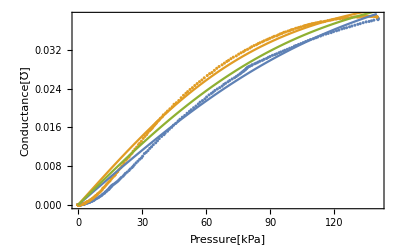

```mathematica
Show[ListPlot[{gloading,gunloading},Frame->True,FrameLabel->{"Pressure[kPa]","Conductance[℧]"}],Plot[Evaluate[gfunc/.#&/@{fitload,fitunload,fit}],{p,0,140}]]
```